# NG^4 T_05. Линейная разделимость, опорные векторы, повышение размерности

02-март-2023
Шклярик Вера

## Section. Логический оператор AND как пример линейно разделимых классов

### Section.Subsection. Фазовое пространство

```mathematica
Tuples[{False, True},2]
And@@@%
{X,Y}= {%%, %}/.{False->-1, True->1}
```

{{False,False},{False,True},{True,False},{True,True}}

{False,False,False,True}

{{{-1,-1},{-1,1},{1,-1},{1,1}},{-1,-1,-1,1}}

3

1

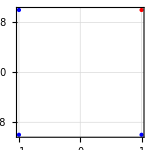

```mathematica
Length[iCold = Flatten@Position[Y,-1]]
Length[iWarm= Flatten@Position[Y,1]]
Fig0 =Graphics[{PointSize@Large, Blue, Point@X⟦iCold⟧, Red, Point@X⟦iWarm⟧}, ImageSize->150, Frame->True , PlotRange->2, GridLines->Automatic]
```

### Section.Subsection. Разделительная полоса

```mathematica
ClearAll[SVM];
SVM[W_?VectorQ, W0_]:=W.#-W0&;
SVM[W_?VectorQ]:=W.Flatten@{#,-1}&;
```

```mathematica
SVM[{2,-3},-1]@{2,1}
SVM[{2,-3,-1}]@{2,1}
```

2

2

```mathematica
W = RandomReal[{-2,2},3]
```

{-1.63819,-0.581672,0.546255}

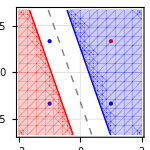

```mathematica
Show[Fig0,ContourPlot[SVM[W]@{x,y},{x,-2,2},{y,-2,2}, Contours->{-1,0,1}, ContourStyle->{Opacity[1,Blue], Dashed, Opacity[1,Red]}, ContourShading->{Opacity[0.2,Blue],None, None, Opacity[0.2,Red]}]]
```

## Section. Задача условной оптимизации

```mathematica
#.#&@{w1,w2}
MapThread[#2 ({w1,w2}.#1-w0)>=1&,{X,Y}]
Flatten@{%%,%}
Last@FindMinimum[%, {w1,w2,w0}]
W = {w1,w2,w0}/.%
```

w1^2+w2^2

{w0+w1+w2≥1,w0+w1-w2≥1,w0-w1+w2≥1,-w0+w1+w2≥1}

{w1^2+w2^2,w0+w1+w2≥1,w0+w1-w2≥1,w0-w1+w2≥1,-w0+w1+w2≥1}

{w1→1.,w2→1.,w0→1.}

{1.,1.,1.}

## Section. Логический оператор XOR и повышение размерности фазового пространства

```mathematica
Tuples[{False, True},2]
Xor@@@%
{X,Y}= {%%, %}/.{False->-1, True->1}
```

{{False,False},{False,True},{True,False},{True,True}}

{False,True,True,False}

{{{-1,-1},{-1,1},{1,-1},{1,1}},{-1,1,1,-1}}

2

2

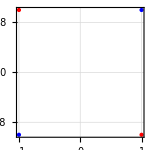

```mathematica
Length[iCold = Flatten@Position[Y,-1]]
Length[iWarm= Flatten@Position[Y,1]]
Fig0 =Graphics[{PointSize@Large, Blue, Point@X⟦iCold⟧, Red, Point@X⟦iWarm⟧}, ImageSize->150, Frame->True , PlotRange->2, GridLines->Automatic]
```

### Section.Subsection. Разделительная полоса

```mathematica
ClearAll[Elevate3];
Elevate3[{x1_, x2_}]:= Flatten@{x1,x2,{x1+x2}^2/4}
```

```mathematica
W = RandomReal[{-2,2},4]
```

{-1.68644,-1.04236,-0.219649,-1.09991}

```mathematica
Elevate3@{x,y}
```

{x,y,1/4 (x+y)^2}

```mathematica
XX = Elevate3/@X;
```

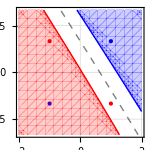

```mathematica
Show[Fig0,ContourPlot[SVM[W]@Elevate3@{x,y},{x,-2,2},{y,-2,2}, Contours->{-1,0,1}, ContourStyle->{Opacity[1,Blue], Dashed, Opacity[1,Red]}, ContourShading->{Opacity[0.2,Blue],None, None, Opacity[0.2,Red]}]]
```

```mathematica
Dynamic[{Show[Fig0,ContourPlot[SVM[W]@Elevate3@{x,y},{x,-2,2},{y,-2,2},Contours->{-1,0,1},ContourStyle->{Opacity[1,Blue],Dashed,Opacity[1,Red]},ContourShading->{Opacity[0.2,Blue],None,None,Opacity[0.2,Red]}]],Show[Graphics3D[{PointSize@Medium,Blue,Point@XX[[iCold]],Red,Point@XX[[iWarm]]},ImageSize->150,PlotRange->2],ContourPlot3D[SVM[W]@{x,y,z},{x,-2,2},{y,-2,2},{z,-2,2},Contours->{-1,0,1},ContourStyle->{Opacity[0.5,Blue],Opacity[0.5,Gray],Opacity[0.5,Red]},Mesh->False,BoundaryStyle->None]]},TrackedSymbols:>{W}];
```

```mathematica
#.#&@{w1,w2,w3};
MapThread[#2 ({w1,w2,w3}.#1-w0)>=1&,{XX,Y}];
Flatten@{%%,%};
Last@FindMinimum[%, {w1,w2,w3,w0}];
W = {w1,w2,w3,w0}/.%;
```

## Section. Метод опорных векторов

### Section.Subsection. Исходное фазовое пространство

```mathematica
Tuples[{False, True},2]
Xor@@@%
{X,Y}= {%%, %}/.{False->-1, True->1}
```

{{False,False},{False,True},{True,False},{True,True}}

{False,True,True,False}

{{{-1,-1},{-1,1},{1,-1},{1,1}},{-1,1,1,-1}}

```mathematica
Length[iCold = Flatten@Position[Y,-1]]
Length[iWarm= Flatten@Position[Y,1]]
Fig0 =Graphics[{PointSize@Large, Blue, Point@X⟦iCold⟧, Red, Point@X⟦iWarm⟧}, ImageSize->150, Frame->True , PlotRange->2, GridLines->Automatic]
```

2

2

-Graphics-

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Dimensions[Train = Import["NG23T05Problem.xlsx", {"Sheets","Шклярик Вера" }]]
```

{4753,3}

```mathematica
Train⟦;;3⟧;
Map[Dimensions,{X= Train[[2;;,{1,2}]],Y=Rationalize@ Train[[2;;,3]]}]
```

{{4752,2},{4752}}

705

4047

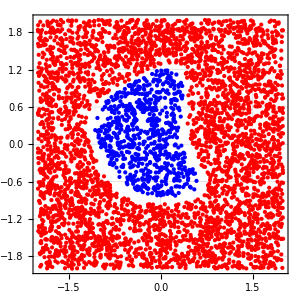

```mathematica
Length[iCold = Flatten@Position[Y,-1]]
Length[iWarm= Flatten@Position[Y,1]]
Fig0 =Graphics[{PointSize@Small, Blue, Point@X⟦iCold⟧, Red, Point@X⟦iWarm⟧}, ImageSize->300, Frame->True , PlotRange->2, GridLines->Automatic]
```

### Section.Subsection. Расширенное фазовое пространство

```mathematica
Flatten@Table[x1^(n-i)x2^i, {n,1,4}, {i,0,n}]
```

{x1,x2,x1^2,x1 x2,x2^2,x1^3,x1^2 x2,x1 x2^2,x2^3,x1^4,x1^3 x2,x1^2 x2^2,x1 x2^3,x2^4}

```mathematica
ClearAll[Elevate14];
Elevate14= With[{$=Flatten@Table[#1^(n-i)#2^i, {n,1,4}, {i,0,n}]},$&]
```

{#1,#2,#1^2,#1 #2,#2^2,#1^3,#1^2 #2,#1 #2^2,#2^3,#1^4,#1^3 #2,#1^2 #2^2,#1 #2^3,#2^4}&

```mathematica
Elevate14[3,-1]
```

{3,-1,9,-3,1,27,-9,3,-1,81,-27,9,-3,1}

```mathematica
Dimensions[XX=Elevate14@@@X]
```

{4752,14}

### Section.Subsection. Пошаговое выполнение алгоритма SVM

Рис 5. Построение разделительной полосы методом опорных векторов

### Section.Subsection. Разделительная полоса

```mathematica
W
```

{-7.57887×10^-17,-8.62734×10^-17,-2.,-1.}

```mathematica
iS
```

iS

```mathematica
ClearAll[SVM];
SVM[W_?VectorQ][X_]:=W.Flatten@{X,-1}
```

## Section. Опорные точки

```mathematica
Dimensions[Train = Import["NG23T05Problem.xlsx", {"Sheets","Train" }]]
```

{181,3}

```mathematica
Train⟦;;3⟧;
Map[Dimensions,{X= Train[[2;;,{1,2}]],Y=Rationalize@ Train[[2;;,3]]}]
```

{{180,2},{180}}

133

47

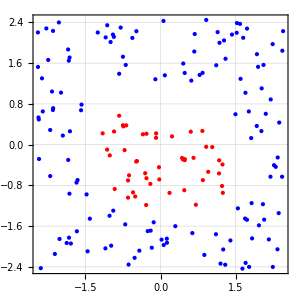

```mathematica
Length[iCold = Flatten@Position[Y,-1]]
Length[iWarm= Flatten@Position[Y,1]]
Fig0 =Graphics[{PointSize@Medium, Blue, Point@X⟦iCold⟧, Red, Point@X⟦iWarm⟧}, ImageSize->300, Frame->True , PlotRange->2, GridLines->Automatic]
```

```mathematica
ClearAll[Elevate5];
Elevate5= With[{$=Flatten@Table[#1^(n-i)#2^i, {n,1,2}, {i,0,n}]},$&]
```

{#1,#2,#1^2,#1 #2,#2^2}&

```mathematica
Dimensions[XX = Elevate5@@@X]
```

{180,5}

```mathematica
(*{iS, iC} = TakeDrop[RandomInteger[{1,Length@Y},4],2]*)
```

```mathematica
(*CreatePalette@Show[Fig0, Graphics[{AbsoluteThickness@4,Green, Dynamic[Circle[#,Offset@4]&/@X⟦iS⟧],Gray, Dynamic[Circle[#,Offset@4]&/@X⟦iC⟧]}]]*)
```

```mathematica
W = RandomReal[{-2,2},6]
```

{-1.02517,1.57721,1.59575,-1.41202,0.453618,1.85278}

```mathematica
Elevate5[x,y]
```

{x,y,x^2,x y,y^2}

```mathematica
CreatePalette[Dynamic[Show[Fig0, Graphics[{AbsoluteThickness@4,Green, Circle[#,Offset@4]&/@X⟦iS⟧,Gray, Circle[#,Offset@4]&/@X⟦iC⟧}],ContourPlot[SVM[W]@Elevate5[x,y],{x,-2.6,2.6},{y,-2.6,2.6}, Contours->{-1,0,1}, ContourStyle->{Opacity[1,Blue], Dashed, Opacity[1,Red]}, ContourShading->{Opacity[0.2,Blue],None, None, Opacity[0.2,Red]}],PlotRange->All], TrackedSymbols:>{iS,iC,W}], WindowTitle->Dynamic@ToString@StringForm["Support = ``, Cost = ``, Step = ``",Length@iS, Length@iC,Step]]
```

## Section. Множители Лагранжа и формулировка двойственной задачи

```mathematica
ClearAll[SVM];
SVM[W_?VectorQ][X_]:=W.Flatten@{X,-1}
```

```mathematica
Outer[Times, #,#]&@Y[[iS]];
#.(#ᵀ)&@XX[[iS]];
```

```mathematica
Dimensions@XX[[iS]]
```

{4,5}

```mathematica
Dimensions[Q=Outer[Times, #,#]&@Y[[iS]](#.(#ᵀ)&@XX[[iS]])]
```

{4,4}

```mathematica
Λ = Table[Subscript[λ, n], {n,iS}]
```

{λ_73,λ_90,λ_140,λ_150}

```mathematica
-Total@Λ+Q.Λ.Λ//Expand;
```

```mathematica
{-Total@Λ+Q.Λ.Λ//Expand, Y[[iS]].Λ==0}
FindArgMin[%,Λ]
```

{-λ_73+8.53189 λ_73^2-λ_90+5.75208 λ_73 λ_90+10.6947 λ_90^2-λ_140-7.70224 λ_73 λ_140-2.12875 λ_90 λ_140+2.19762 λ_140^2-λ_150-2.36839 λ_73 λ_150-11.3108 λ_90 λ_150+0.462676 λ_140 λ_150+3.24289 λ_150^2,-λ_73-λ_90+λ_140+λ_150==0}

{0.206572,0.365383,0.119713,0.452242}

```mathematica
solΛ = FindArgMin[{-Total@Λ+Q.Λ.Λ//Expand, Y[[iS]].Λ==0},Λ]
```

{0.206572,0.365383,0.119713,0.452242}

## Section. Последовательный метод активных ограничений

### Section.Subsection. Инициализация множества опорных точек

```mathematica
iS = {sCold = RandomChoice@iCold}
```

{33}

```mathematica
iS = {sCold , sWarm = iWarm[[First@Nearest[XX[[iWarm]]->"Index",XX[[sCold]]]]]}
```

{33,70}

```mathematica
iS = {sCold =iCold[[First@Nearest[XX[[iCold]]->"Index",XX[[sWarm]]]]], sWarm }
```

{73,70}

```mathematica
Step = 0;
1;
iS = Flatten@Table[FixedPoint[(iS = {sCold , sWarm = iWarm[[First@Nearest[XX[[iWarm]]->"Index",XX[[sCold]]]]]};iS = {sCold =iCold[[First@Nearest[XX[[iCold]]->"Index",XX[[sWarm]]]]], sWarm })&,iS = {sCold = RandomChoice@iCold}],{%}]
```

{128,99}

### Section.Subsection. Построение разделительной полосы

```mathematica
Step=Step+1;
Λ = Table[Subscript[λ, n], {n,iS}]
Dimensions[Q=0.5 Outer[Times, #,#]&@Y[[iS]](#.(#ᵀ)&@XX[[iS]])]
solΛ = FindArgMin[{-Total@Λ+Q.Λ.Λ//Expand, Y[[iS]].Λ==0},Λ]
```

{λ_128,λ_99}

{2,2}

{1.05124,1.05124}

```mathematica
W1 = Dot[solΛ Y[[iS]], XX[[iS]]];
```

```mathematica
w0 = Median[XX[[iS]].W1 - Y[[iS]]];
```

```mathematica
W = Flatten@{W1 = Dot[solΛ Y[[iS]], XX[[iS]]],w0 = Median[XX[[iS]].W1 - Y[[iS]]] }
```

{0.328487,-0.345632,-0.901428,0.62171,-0.310336,-2.83683}

### Section.Subsection. Проверка опорных точек

```mathematica
iC= Extract[iS,Position[solΛ,Min@solΛ,1,1]]
```

{90}

### Section.Subsection. Ложная опорная точка

```mathematica
{iS = Delete[iS,Position[solΛ,Min@solΛ,1,1]],iC = {}}
```

{{150},{}}

### Section.Subsection. Отступы

```mathematica
Length[iO = Complement[Range@Length@Y,iS]]
```

179

```mathematica
Dimensions[M =XX[[iO]].W1 - w0];
```

```mathematica
Min@M;
Position[M,%,1,1];
iC = Extract[iO,%];
```

```mathematica
Length[iO = Complement[Range@Length@Y,iS]]
M =XX[[iO]].W1 - w0;
iC = Extract[iO,Position[M,Min@M,1,1]]
```

179

{177}

### Section.Subsection. Новая опорная точка

```mathematica
{iS = Union[iS,iC],iC = {}}
```

{{150,177},{}}

### Section.Subsection. Конец алгоритма

Для удобства перенесем основные ячейки, участвующие в выполнении алгоритма.

```mathematica
Step = 0;
2;
iS = Flatten@Table[FixedPoint[(iS = {sCold , sWarm = iWarm[[First@Nearest[XX[[iWarm]]->"Index",XX[[sCold]]]]]};iS = {sCold =iCold[[First@Nearest[XX[[iCold]]->"Index",XX[[sWarm]]]]], sWarm })&,iS = {sCold = RandomChoice@iCold}],{%}]
```

{104,92,54,77}

```mathematica
Step = Step+1;
Λ = Table[Subscript[λ, n], {n,iS}]
Dimensions[Q=0.5 Outer[Times, #,#]&@Y[[iS]](#.(#ᵀ)&@XX[[iS]])]
solΛ = FindArgMin[{-Total@Λ+Q.Λ.Λ//Expand, Y[[iS]].Λ==0},Λ]
W = Flatten@{W1 = Dot[solΛ Y[[iS]], XX[[iS]]],w0 = Median[XX[[iS]].W1 - Y[[iS]]] };
```

{λ_64,λ_67,λ_77,λ_90,λ_99,λ_134}

{6,6}

{3.45879,0.75969,2.58887,0.721616,2.0289,1.19706}

```mathematica
iC= Extract[iS,Position[solΛ,Min@solΛ,1,1]]
```

{104}

```mathematica
{iS = Delete[iS,Position[solΛ,Min@solΛ,1,1]],iC = {}}
```

{{64,77,90,99,134},{}}

```mathematica
Length[iO = Complement[Range@Length@Y,iS]]
M = MapThread[#2SVM[W]@#1&,{XX[[iO]],Y[[iO]]}];
iC = Extract[iO,Position[M,Min@M,1,1]]
```

175

{67}

```mathematica
{iS = Union[iS,iC],iC = {}}
```

{{64,67,77,90,99,134},{}}

Начиная с опорных точек под номерами {104,92,54,77} построила границу за 11 шагов.